### Start choosing the example:

```mathematica
t=13;
beta = 1;
A = 0;
g[x]
```

x

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesData.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,1,0},{0,0,0,1},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{{1,2,4,S1},{1,3,4,S2},{4,2,1,S3},{4,3,1,S4}}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->10,U1->5,S1->100,S2->0,S3->0,S4->0}];//Timing
MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]
MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]]
```

DataToEquations: Triangle inequalities for switching costs: {True,True,True,True}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.18862 seconds to reduce with NewReduce!

DataToEquations: After NewReduce, the system is:
j469==0&&j470==10&&j475==0&&u497==25&&u498==25&&u499==5&&u500==15&&u502==25
and the rules are:
<|j474→10,u507→5,j471→j469,j472→j470,j473→10,j476→-10+j469+j470-j475,j477→j475,j478→-10+j469+j470-j475,j479→0,j480→0,jt481→j475,jt482→0,jt483→-10+j469+j470-j475,jt484→0,jt485→10-j470+j475,jt486→j470-j475,jt487→j469,jt488→j475,jt489→j470,jt490→-10+j469+j470-j475,jt491→-10+j469+j470-j475,jt492→10-j470+j475,jt493→j475,jt494→j470-j475,jt495→0,jt496→0,u501→5,u503→-j469+j475+u497,u504→-10+j469-j475+u498,u505→-j469+j475+u499,u506→-10+j469-j475+u500,u508→u502|>

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.233356,Null}

<|{1,1->2}→25,{1,1->3}→25,{2,2->4}→5,{3,3->4}→15,{4,4->ex468}→5,{en467,en467->1}→25,{2,1->2}→25,{3,1->3}→15,{4,2->4}→5,{4,3->4}→5,{ex468,4->ex468}→5,{1,en467->1}→25|>

<|{2,1->2}→0,{3,1->3}→10,{4,2->4}→0,{4,3->4}→10,{ex468,4->ex468}→10,{1,en467->1}→10,{1,1->2}→0,{1,1->3}→0,{2,2->4}→0,{3,3->4}→0,{4,4->ex468}→0,{en467,en467->1}→0|>

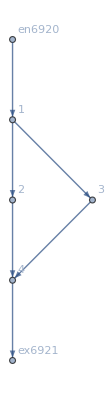

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j469→0,j470→10,j471→0,j472→10,j473→10,j474→10,j475→0,j476→0,j477→0,j478→0,j479→0,j480→0,jt481→0,jt482→0,jt483→0,jt484→0,jt485→0,jt486→10,jt487→0,jt488→0,jt489→10,jt490→0,jt491→0,jt492→0,jt493→0,jt494→10,jt495→0,jt496→0,u497→25,u498→25,u499→5,u500→15,u501→5,u502→25,u503→25,u504→15,u505→5,u506→5,u507→5,u508→25|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j469→0,j470→10.,j471→0,j472→10.,j473→10,j474→10,j475→0,j476→0.,j477→0,j478→0.,j479→0,j480→0,jt481→0,jt482→0,jt483→0.,jt484→0,jt485→0.,jt486→10.,jt487→0,jt488→0,jt489→10.,jt490→0.,jt491→0.,jt492→0.,jt493→0,jt494→10.,jt495→0,jt496→0,u497→10.4288,u498→10.4288,u499→5.,u500→7.71442,u501→5,u502→10.4288,u503→10.4288,u504→7.71442,u505→5.,u506→5.,u507→5,u508→10.4288|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j469→0,j470→10.,j471→0,j472→10.,j473→10,j474→10,j475→0,j476→0.,j477→0,j478→0.,j479→0,j480→0,jt481→0,jt482→0,jt483→0.,jt484→0,jt485→0.,jt486→10.,jt487→0,jt488→0,jt489→10.,jt490→0.,jt491→0.,jt492→0.,jt493→0,jt494→10.,jt495→0,jt496→0,u497→10.9397,u498→10.9397,u499→5.,u500→7.96984,u501→5,u502→10.9397,u503→10.9397,u504→7.96984,u505→5.,u506→5.,u507→5,u508→10.9397|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.9681×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.9681×10^-17

<|j469→0,j470→10.,j471→0,j472→10.,j473→10,j474→10,j475→0,j476→0.,j477→0,j478→0.,j479→0,j480→0,jt481→0,jt482→0,jt483→0.,jt484→0,jt485→0.,jt486→10.,jt487→0,jt488→0,jt489→10.,jt490→0.,jt491→0.,jt492→0.,jt493→0,jt494→10.,jt495→0,jt496→0,u497→12.2536,u498→12.2536,u499→5.,u500→8.62682,u501→5,u502→12.2536,u503→12.2536,u504→8.62682,u505→5.,u506→5.,u507→5,u508→12.2536|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j469→0,j470→10.,j471→0,j472→10.,j473→10,j474→10,j475→0,j476→0.,j477→0,j478→0.,j479→0,j480→0,jt481→0,jt482→0,jt483→0.,jt484→0,jt485→0.,jt486→10.,jt487→0,jt488→0,jt489→10.,jt490→0.,jt491→0.,jt492→0.,jt493→0,jt494→10.,jt495→0,jt496→0,u497→21.6007,u498→21.6007,u499→5.,u500→13.3004,u501→5,u502→21.6007,u503→21.6007,u504→13.3004,u505→5.,u506→5.,u507→5,u508→21.6007|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.50729×10^-14,ComplexInfinity]

<|j469→0,j470→10,j471→0,j472→10,j473→10,j474→10,j475→0,j476→0,j477→0,j478→0,j479→0,j480→0,jt481→0,jt482→0,jt483→0,jt484→0,jt485→0,jt486→10,jt487→0,jt488→0,jt489→10,jt490→0,jt491→0,jt492→0,jt493→0,jt494→10,jt495→0,jt496→0,u497→25,u498→25,u499→5,u500→15,u501→5,u502→25,u503→25,u504→15,u505→5,u506→5,u507→5,u508→25|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j469→0,j470→10.,j471→0,j472→10.,j473→10,j474→10,j475→0,j476→0.,j477→0,j478→0.,j479→0,j480→0,jt481→0,jt482→0,jt483→0.,jt484→0,jt485→0.,jt486→10.,jt487→0,jt488→0,jt489→10.,jt490→0.,jt491→0.,jt492→0.,jt493→0,jt494→10.,jt495→0,jt496→0,u497→35.889,u498→35.889,u499→5.,u500→20.4445,u501→5,u502→35.889,u503→35.889,u504→20.4445,u505→5.,u506→5.,u507→5,u508→35.889|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j469→0,j470→10.,j471→0,j472→10.,j473→10,j474→10,j475→0,j476→0.,j477→0,j478→0.,j479→0,j480→0,jt481→0,jt482→0,jt483→0.,jt484→0,jt485→0.,jt486→10.,jt487→0,jt488→0,jt489→10.,jt490→0.,jt491→0.,jt492→0.,jt493→0,jt494→10.,jt495→0,jt496→0,u497→78.6806,u498→78.6806,u499→5.,u500→41.8403,u501→5,u502→78.6806,u503→78.6806,u504→41.8403,u505→5.,u506→5.,u507→5,u508→78.6806|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.326995

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.326995

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.326995

«7 more identical outputs»

<|j469→0,j470→10.,j471→0,j472→10.,j473→10,j474→10,j475→0,j476→0.,j477→0,j478→0.,j479→0,j480→0,jt481→0,jt482→0,jt483→0.,jt484→0,jt485→0.,jt486→10.,jt487→0,jt488→0,jt489→10.,jt490→0.,jt491→0.,jt492→0.,jt493→0,jt494→10.,jt495→0,jt496→0,u497→83.5222,u498→83.5222,u499→5.33377,u500→44.2611,u501→5,u502→83.5222,u503→83.1884,u504→44.2611,u505→5.,u506→5.,u507→5,u508→83.5222|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.09631

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00822

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00006

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«4 more identical outputs»

<|j469→0,j470→3.11859×10^207,j471→0,j472→3.11859×10^207,j473→10,j474→10,j475→3.11859×10^207,j476→-10.,j477→3.11859×10^207,j478→-10.,j479→0,j480→0,jt481→3.11859×10^207,jt482→0,jt483→-10.,jt484→0,jt485→0.,jt486→0.,jt487→0,jt488→3.11859×10^207,jt489→3.11859×10^207,jt490→-10.,jt491→-10.,jt492→0.,jt493→3.11859×10^207,jt494→0.,jt495→0,jt496→0,u497→0.,u498→0.,u499→0.,u500→0.,u501→5,u502→0.,u503→0.,u504→0.,u505→5.,u506→5.,u507→5,u508→0.|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],4,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.01335

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00004

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

<|j469→0,j470→2.09673×10^18,j471→0,j472→2.09673×10^18,j473→10,j474→10,j475→2.09673×10^18,j476→-10.,j477→2.09673×10^18,j478→-10.,j479→0,j480→0,jt481→2.09673×10^18,jt482→0,jt483→-10.,jt484→0,jt485→0.,jt486→0.,jt487→0,jt488→2.09673×10^18,jt489→2.09673×10^18,jt490→-10.,jt491→-10.,jt492→0.,jt493→2.09673×10^18,jt494→0.,jt495→0,jt496→0,u497→5.64184×10^11,u498→5.64184×10^11,u499→2.82092×10^11,u500→2.82092×10^11,u501→5,u502→5.64184×10^11,u503→2.82092×10^11,u504→2.82092×10^11,u505→5.,u506→5.,u507→5,u508→5.64184×10^11|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00113

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«3 more identical outputs»

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[√(2 Abs[-1.365077773379×10^369-1. j469+1. j475-IntM[j469-j475]]^2+2 Abs[1.36507777337899×10^369+1. j469-1. j475-IntM[10-j469+j475]]^2),(√(2 Abs[-1.365077773379×10^369-1. j469+1. j475-IntM[j469-j475]]^2+2 Abs[1.36507777337899×10^369+1. j469-1. j475-IntM[10-j469+j475]]^2))/(√(Abs[-1.36507777337899×10^369+0. j469+0. j475]^2+2 Abs[1.36507777337899×10^369+0. j469+0. j475]^2+Abs[-1.365077773379×10^369+0. j469+0. j475]^2)),(√(2 Abs[-1.365077773379×10^369-1. j469+1. j475-IntM[j469-j475]]^2+2 Abs[1.36507777337899×10^369+1. j469-1. j475-IntM[10-j469+j475]]^2))/(√(2 Abs[j469-j475+IntM[j469-j475]]^2+2 Abs[10-j469+j475+IntM[10-j469+j475]]^2))]

ReplaceAll::reps: {u497==u502&&u498==u502&&u500==u504&&u505==5&&u506==5&&j469-j475-u497+u503==j469-j475+IntM[j469-j475]&&10-j469+j475-u498+u504==10-j469+j475+IntM[10-j469+j475]&&j469-j475-u499+u505==j469-j475+IntM[j469-j475]&&10-j469+j475-u500+u506==10-j469+j475+IntM[10-j469+j475]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

AssociateTo::invlb: The argument u497==u502&&u498==u502&&u500==u504&&u505==5&&u506==5&&j469-j475-u497+u503==j469-j475+IntM[j469-j475]&&10-j469+j475-u498+u504==10-j469+j475+IntM[10-j469+j475]&&j469-j475-u499+u505==j469-j475+IntM[j469-j475]&&10-j469+j475-u500+u506==10-j469+j475+IntM[10-j469+j475] is not a list, Rule, or Association.

ReplaceAll::reps: {u497==u502&&u498==u502&&u500==u504&&u505==5&&u506==5&&j469-j475-u497+u503==j469-j475+IntM[j469-j475]&&10-j469+j475-u498+u504==10-j469+j475+IntM[10-j469+j475]&&j469-j475-u499+u505==j469-j475+IntM[j469-j475]&&10-j469+j475-u500+u506==10-j469+j475+IntM[10-j469+j475]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted

```mathematica
alpha = 1.99;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00006

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«2 more identical outputs»

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[√(2 Abs[1.6442466836797×10^366-1. j469+1. j475-IntM[j469-j475]]^2+2 Abs[-1.64424668367967×10^366+1. j469-1. j475-IntM[10-j469+j475]]^2),(√(2 Abs[1.6442466836797×10^366-1. j469+1. j475-IntM[j469-j475]]^2+2 Abs[-1.64424668367967×10^366+1. j469-1. j475-IntM[10-j469+j475]]^2))/(√(Abs[-1.64424668367967×10^366+0. j469+0. j475]^2+Abs[1.64424668367967×10^366+0. j469+0. j475]^2+Abs[-1.64424668367967×10^366+0. j469+0. j475]^2+Abs[1.6442466836797×10^366+0. j469+0. j475]^2)),(√(2 Abs[1.6442466836797×10^366-1. j469+1. j475-IntM[j469-j475]]^2+2 Abs[-1.64424668367967×10^366+1. j469-1. j475-IntM[10-j469+j475]]^2))/(√(2 Abs[j469-j475+IntM[j469-j475]]^2+2 Abs[10-j469+j475+IntM[10-j469+j475]]^2))]

ReplaceAll::reps: {u497==u502&&u498==u502&&u500==u504&&u505==5&&u506==5&&j469-j475-u497+u503==j469-j475+IntM[j469-j475]&&10-j469+j475-u498+u504==10-j469+j475+IntM[10-j469+j475]&&j469-j475-u499+u505==j469-j475+IntM[j469-j475]&&10-j469+j475-u500+u506==10-j469+j475+IntM[10-j469+j475]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

AssociateTo::invlb: The argument u497==u502&&u498==u502&&u500==u504&&u505==5&&u506==5&&j469-j475-u497+u503==j469-j475+IntM[j469-j475]&&10-j469+j475-u498+u504==10-j469+j475+IntM[10-j469+j475]&&j469-j475-u499+u505==j469-j475+IntM[j469-j475]&&10-j469+j475-u500+u506==10-j469+j475+IntM[10-j469+j475] is not a list, Rule, or Association.

ReplaceAll::reps: {u497==u502&&u498==u502&&u500==u504&&u505==5&&u506==5&&j469-j475-u497+u503==j469-j475+IntM[j469-j475]&&10-j469+j475-u498+u504==10-j469+j475+IntM[10-j469+j475]&&j469-j475-u499+u505==j469-j475+IntM[j469-j475]&&10-j469+j475-u500+u506==10-j469+j475+IntM[10-j469+j475]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00004

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00004

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00004

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00004

<|j469→225.,j470→0,j471→225.,j472→0,j473→10,j474→10,j475→0,j476→215.,j477→0,j478→215.,j479→0,j480→0,jt481→0,jt482→0,jt483→215.,jt484→0,jt485→10,jt486→0,jt487→225.,jt488→0,jt489→0,jt490→215.,jt491→215.,jt492→10,jt493→0,jt494→0,jt495→0,jt496→0,u497→555.,u498→555.,u499→230.,u500→280.,u501→5,u502→555.,u503→330.,u504→280.,u505→5.,u506→5.,u507→5,u508→555.|>